# b = 1 LRW Fractal Dimension on 3d square Lattice

## myMantissaExponent[]

```mathematica
myMantissaExponent[expr_]:=Module[{mant,exp},
{mant,exp}=MantissaExponent[expr];
mant*=10;exp-=1;
{mant,exp}
]
```

## With all the points from the CLUSTER “b=1.000000-LRW-3d-square-lattice-data-3-101.csv” & “b=1.000000-LRW-3d-square-lattice-data-103-201.csv”

```mathematica
data=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b=1.000000-LRW-3d-square-lattice-data-3-101.csv"}],"CSV"],2];
```

```mathematica
data2=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b=1.000000-LRW-3d-square-lattice-data-103-201.csv"}],"CSV"],2];
```

```mathematica
joinedData=Join[data,data2];
```

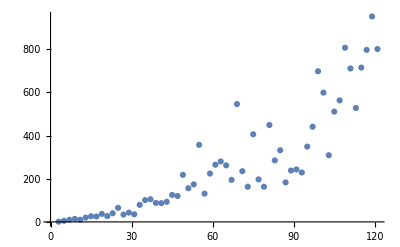

```mathematica
ListPlot[joinedData]
```

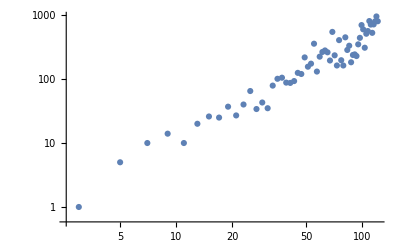

```mathematica
ListLogLogPlot[joinedData]
```

```mathematica
FindFit[Log[joinedData],a+df *x,{a,df},x]
```

{a→-1.3098,df→1.61366}

```mathematica
lm=LinearModelFit[Log[joinedData],x,x]
```

FittedModel[…]

```mathematica
expectedFractalDim=1.624;
ExpectedPlot=Plot[expectedFractalDim*x-2,{x,0,1000},PlotStyle->Green];
```

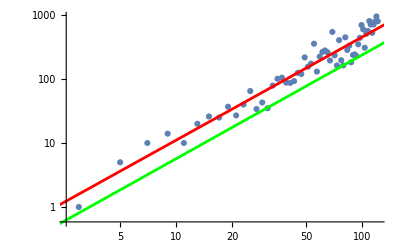

d_f=1.61366

```mathematica
Show[ListLogLogPlot[joinedData],
Plot[lm[x],{x,0,1000},PlotStyle->Red],ExpectedPlot
]
Print[ "d_f=",df/.FindFit[Log[joinedData],a+df *x,{a,df},x]]
```

THIS IS NOT EQUAL TO 1.62400, BUT VERY CLOSE TO IT!!!!

#### Drop the first few

```mathematica
dropped=Drop[joinedData,5];
lm=LinearModelFit[Log[dropped],x,x]
```

FittedModel[…]

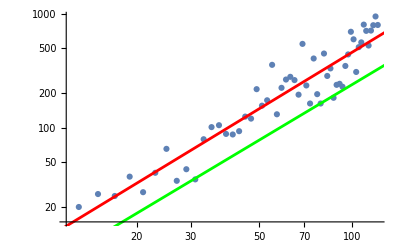

d_f=1.65221

```mathematica
Show[ListLogLogPlot[dropped],
Plot[lm[x],{x,0,1000},PlotStyle->Red],ExpectedPlot
]
Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x]]
```

It doesn’t improve it much.

## With all the points from the CLUSTER: “b=1.000000-LRW-3d-square-lattice-data-3-101.csv” TO 501 almost

### Raw data

```mathematica
data1=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b1LRW\\b=1.000000-LRW-3d-square-lattice-data-3-101.csv"}],"CSV"],2];
```

```mathematica
data2=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b1LRW\\b=1.000000-LRW-3d-square-lattice-data-103-201.csv"}],"CSV"],2];
```

```mathematica
data3=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b1LRW\\b=1.000000-LRW-3d-square-lattice-data-203-301.csv"}],"CSV"],2];
```

```mathematica
data4=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b1LRW\\b=1.000000-LRW-3d-square-lattice-data-303-401.csv"}],"CSV"],2];
```

```mathematica
data5=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b1LRW\\b=1.000000-LRW-3d-square-lattice-data-403-501.csv"}],"CSV"],2];
```

```mathematica
rawData=joinedData=Join[data1,data2,data3,data4,data5];
```

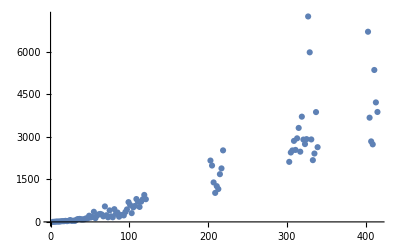

```mathematica
ListPlot[joinedData]
```

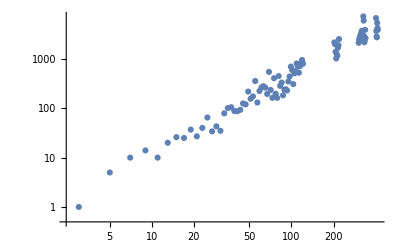

```mathematica
ListLogLogPlot[joinedData]
```

```mathematica
Clear[x]
```

```mathematica
FindFit[Log[joinedData],a+df *x,{a,df},x]
```

{a→-1.29848,df→1.61133}

```mathematica
lm=LinearModelFit[Log[joinedData],x,x]
```

FittedModel[…]

```mathematica
lm["ParameterErrors"]
```

{0.143486,0.0306181}

```mathematica
expectedFractalDim=1.624;
ExpectedPlot=Plot[expectedFractalDim*x-2,{x,0,1000},PlotStyle->Green];
```

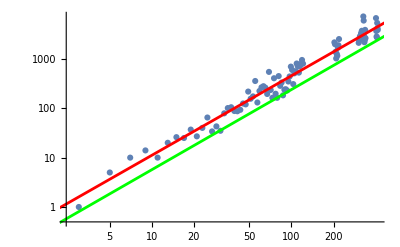

d_f=1.61133
Result from the litterature: expectedFractalDim

```mathematica
Show[ListLogLogPlot[joinedData],
Plot[lm[x],{x,0,1000},PlotStyle->Red],ExpectedPlot
]
Print[ "d_f=",df/.FindFit[Log[joinedData],a+df *x,{a,df},x],"
Result from the litterature: expectedFractalDim"]
```

THIS IS NOT EQUAL TO 1.62400, BUT VERY CLOSE TO IT!!!!

### Drop the first few

```mathematica
dropped=Drop[rawData,6];
lm=LinearModelFit[Log[dropped],x,x]
```

FittedModel[…]

```mathematica
lm["ParameterErrors"]
```

{0.184322,0.0382974}

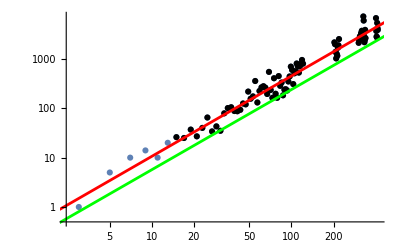

d_f=1.6287
Result from the litterature: 1.624

```mathematica
Show[ListLogLogPlot[joinedData],ListLogLogPlot[dropped,PlotStyle->Black],
Plot[lm[x],{x,0,1000},PlotStyle->Red],ExpectedPlot
]
Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"
Result from the litterature: ",expectedFractalDim]
```

ALMOST THE SAME AS THE BEST SIMULATION IN THE LITTERATURE

### Get stdDev by using Kay’s method

#### All the data

```mathematica
joinedData=rawData;
```

```mathematica
empirical=Module[{sampled,lm,a,df,x,slopeData,meanSlope,stdDevSlope},

slopeData=Table[
sampled=RandomSample[Log[joinedData],Floor[Length[joinedData]/2]];

lm=FindFit[sampled,a+df *x,{a,df},x];

df/.lm
,{i,1,10000}];

meanSlope=Mean[slopeData];
stdDevSlope=StandardDeviation [slopeData];

Return[{meanSlope,stdDevSlope}];
];
```

Return[{1.61194,0.0324923}]

```mathematica
empirical
```

{1.61194,0.0324923}

```mathematica
lm=LinearModelFit[Log[joinedData],x,x];
lm["ParameterErrors"]
{meanExact,stdDevExact}={(lm["ParameterTable"]//Normal)[[1,3,2]],lm["ParameterErrors"][[2]]}
dfExact=df/.FindFit[joinedData,a+df *x,{a,df},x]
{mantExact,expExact}=myMantissaExponent[meanExact]
{mantstdDevExact,expstdDevExact}=MantissaExponent[stdDevExact]
```

{0.143486,0.0306181}

{1.61133,0.0306181}

11.0363

{1.61133,0}

{0.306181,-1}

```mathematica
{mantEmp,expEmp}=myMantissaExponent[empirical[[1]]]
```

{1.61194,0}

```mathematica
Print[" The exact value of the slope from the data is (",mantExact,"±",mantstdDevExact,")×",Superscript[10,MantissaExponent[meanExact][[2]]-1], "
 While, by using Kay's procedure, we get (",mantEmp,"±",MantissaExponent[empirical[[2]]][[1]],")×",Superscript[10,expEmp]]
```

The exact value of the slope from the data is (1.61133±0.306181)×10^0
 While, by using Kay's procedure, we get (1.61194±0.324923)×10^0

#### On dropped data

```mathematica
joinedData=dropped;
```

```mathematica
empirical=Module[{sampled,lm,a,df,x,slopeData,meanSlope,stdDevSlope},

slopeData=Table[
sampled=RandomSample[Log[joinedData],Floor[Length[joinedData]/2]];

lm=FindFit[sampled,a+df *x,{a,df},x];

df/.lm
,{i,1,10000}];

meanSlope=Mean[slopeData];
stdDevSlope=StandardDeviation [slopeData];

Return[{meanSlope,stdDevSlope}];
];
```

Return[{1.62888,0.0360592}]

```mathematica
empirical
```

{1.62888,0.0360592}

```mathematica
lm=LinearModelFit[Log[joinedData],x,x];
lm["ParameterErrors"]
{meanExact,stdDevExact}={(lm["ParameterTable"]//Normal)[[1,3,2]],lm["ParameterErrors"][[2]]}
dfExact=df/.FindFit[joinedData,a+df *x,{a,df},x]
{mantExact,expExact}=myMantissaExponent[meanExact]
{mantstdDevExact,expstdDevExact}=MantissaExponent[stdDevExact]
```

{0.184322,0.0382974}

{1.6287,0.0382974}

11.2536

{1.6287,0}

{0.382974,-1}

```mathematica
{mantEmp,expEmp}=myMantissaExponent[empirical[[1]]]
```

{1.62888,0}

```mathematica
Print[" The exact value of the slope from the data is (",mantExact,"±",mantstdDevExact,")×",Superscript[10,MantissaExponent[meanExact][[2]]-1], "
 While, by using Kay's procedure, we get (",mantEmp,"±",MantissaExponent[empirical[[2]]][[1]],")×",Superscript[10,expEmp]]
```

The exact value of the slope from the data is (1.6287±0.382974)×10^0
 While, by using Kay's procedure, we get (1.62888±0.360592)×10^0